# Introduction to Mathematica

## #CA1 #Q5 Signals & Systems Mohammad GharehHasanloo

## Part A

1000000 √2 ⅇ

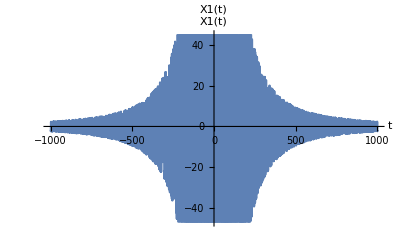

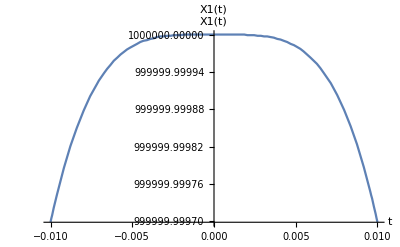

```mathematica
X1[t_,eps_] := (1/eps)*(Sin[Pi*((t/E)^2)]/(Pi*((t/E)^2)))
∫_-Infinity^Infinity (Limit[X1[t,eps],eps->10^(-6)] )ⅆt 
Plot[X1[t],{t,-1000,1000},PlotLabel->"X1(t)",AxesLabel->{"t","X1(t)"}]
Plot[X1[t],{t,-0.01,0.01},PlotLabel->"X1(t)",AxesLabel->{"t","X1(t)"}]
```

```mathematica
X2[t_,eps_] := Piecewise[{{(1-Abs[t]/eps)/eps, Abs[t]≤eps}, {0, Abs[t]>eps}}]
∫_-Infinity^Infinity (Limit[X2[t,eps],eps->10^(-6)] )ⅆt 
Plot[X2[t],{t,-1000,1000},PlotLabel->"X2(t)",AxesLabel->{"t","X2(t)"}]
Plot[X2[t],{t,-0.00001,0.00001},PlotLabel->"X2(t)",AxesLabel->{"t","X2(t)"}]
```

1

-Graphics-

-Graphics-

1

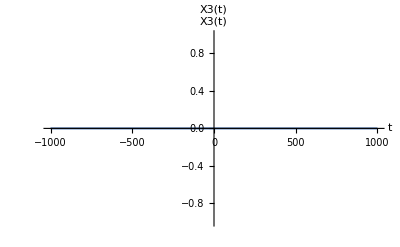

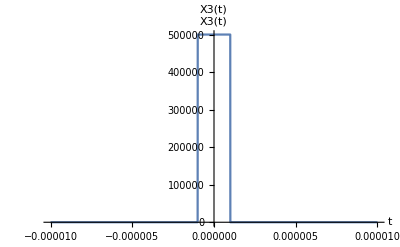

```mathematica
X3[t_,eps_] := (1/(2*eps))*(UnitStep[(t/(2*eps))+1/2]-UnitStep[(t/(2*eps))-1/2])
∫_-Infinity^Infinity (Limit[X3[t,eps],eps->10^(-6)] )ⅆt 
Plot[X3[t],{t,-1000,1000},PlotLabel->"X3(t)",AxesLabel->{"t","X3(t)"}]
Plot[X3[t],{t,-0.00001,0.00001},PlotLabel->"X3(t)",AxesLabel->{"t","X3(t)"}]
```

1

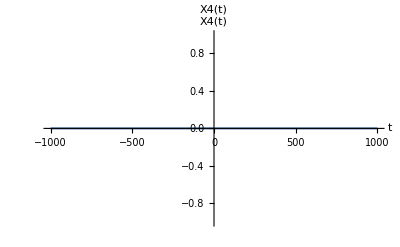

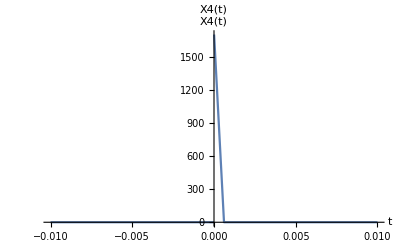

```mathematica
X4[t_,eps_]:=(1/eps)*(Exp[-(t/eps)])*UnitStep[t]
∫_-Infinity^Infinity (Limit[X4[t,eps],eps->10^(-6)] )ⅆt 
Plot[X4[t],{t,-1000,1000},PlotLabel->"X4(t)",AxesLabel->{"t","X4(t)"}]
Plot[X4[t],{t,-0.01,0.01},PlotLabel->"X4(t)",AxesLabel->{"t","X4(t)"}]
```

1

General::munfl: Exp[-4.99959×10^17] is too small to represent as a normalized machine number; precision may be lost.

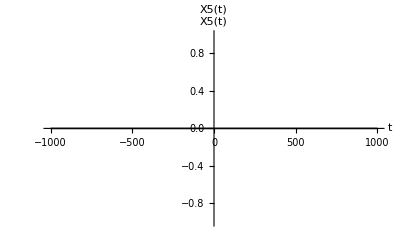

General::munfl: Exp[-499959.] is too small to represent as a normalized machine number; precision may be lost.

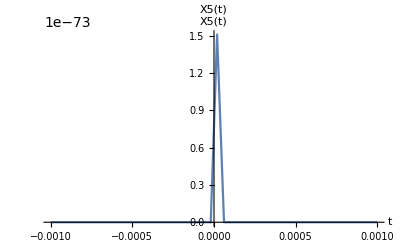

```mathematica
X5[t_,eps_] := Exp[-t^2/(2*(eps)^2)]/(√(2*Pi*(eps)^2))
∫_-Infinity^Infinity (Limit[X5[t,eps],eps->10^(-6)] )ⅆt 
Plot[X5[t],{t,-1000,1000},PlotLabel->"X5(t)",AxesLabel->{"t","X5(t)"}]
Plot[X5[t],{t,-0.001,0.001},PlotLabel->"X5(t)",AxesLabel->{"t","X5(t)"}]
```

## Part B

```mathematica
Export["X1.gif",Animate[X1[t,eps],{eps,10,0.1}]]
```

X1.gif

```mathematica
Export["X2.gif",Animate[X2[t,eps],{eps,10,0.1}]]
```

X2.gif

```mathematica
Export["X3.gif",Animate[X3[t,eps],{eps,10,0.1}]]
```

X3.gif

```mathematica
Export["X4.gif",Animate[X4[t,eps],{eps,10,0.1}]]
```

X4.gif

```mathematica
Export["X5.gif",Animate[X5[t,eps],{eps,10,0.1}]]
```

X5.gif